```mathematica
Clear[z,x,y,s,ϕ,θ]
(*radius of loop kept as s*)
(*permittivity of free space kept as m*)
(l[Theta_]:={s Cos[Theta],s Sin[Theta],0}; (*r' conversion to polar coordinates*)
R={x,y,z}-l[Theta];(*r-r'*)
mod:=Sqrt[R.R];(*taking absolute*)
dl=D[l[Theta],Theta];(*line element*)
Cross[dl,R];)(*cross product*)
integrand=%/(mod^3);(*dividing by the cube of absolute*)
int2= Simplify[integrand/.Thread[{x,y,z}->ρ {Cos[ϕ] Sin[θ],Sin[ϕ] Sin[θ],Cos[θ]}/.ϕ->0],ρ>0&&θ>0&&ϕ>0&&Theta>0&&s>0] (*setting up the integrand. the 10^-7 is to include m/4Pi. current I is currently set to 1 Amp*)
```

{(s ρ Cos[Theta] Cos[θ])/((s^2+ρ^2-2 s ρ Cos[Theta] Sin[θ])^(3/2)),(s ρ Cos[θ] Sin[Theta])/((s^2+ρ^2-2 s ρ Cos[Theta] Sin[θ])^(3/2)),(s (s-ρ Cos[Theta] Sin[θ]))/((s^2+ρ^2-2 s ρ Cos[Theta] Sin[θ])^(3/2))}

```mathematica
int2[[1]] (*this is without the constant mu/Pi*)
```

(s ρ Cos[Theta] Cos[θ])/((s^2+ρ^2-2 s ρ Cos[Theta] Sin[θ])^(3/2))

```mathematica
int2[[3]](*this is without the constant mu/Pi*)
```

(s (s-ρ Cos[Theta] Sin[θ]))/((s^2+ρ^2-2 s ρ Cos[Theta] Sin[θ])^(3/2))

```mathematica
Bx=(10^(-7))2 Assuming[ρ>0&&Pi/2>θ>0&&s>0,Integrate[int2[[1]],{Theta,0,Pi}]](*adding in the constant at the front*)
```

(Cot[θ] ((s^2+ρ^2) EllipticE[(4 s ρ Sin[θ])/(s^2+ρ^2+2 s ρ Sin[θ])]-EllipticK[(4 s ρ Sin[θ])/(s^2+ρ^2+2 s ρ Sin[θ])] (s^2+ρ^2-2 s ρ Sin[θ])))/(5000000 (s^2+ρ^2-2 s ρ Sin[θ]) √(s^2+ρ^2+2 s ρ Sin[θ]))

```mathematica
Bz=(10^(-7)) 2 Assuming[ρ>0&&Pi/2>θ>0&&s>0,Integrate[int2[[3]],{Theta,0,Pi}]](*adding in the constant at the front*)
```

((s^2-ρ^2) EllipticE[(4 s ρ Sin[θ])/(s^2+ρ^2+2 s ρ Sin[θ])]+EllipticK[(4 s ρ Sin[θ])/(s^2+ρ^2+2 s ρ Sin[θ])] (s^2+ρ^2-2 s ρ Sin[θ]))/(5000000 (s^2+ρ^2-2 s ρ Sin[θ]) √(s^2+ρ^2+2 s ρ Sin[θ]))

```mathematica
s=5*10^(-3);(*now setting ring radius after integration*)
Bx
Bz
```

(Cot[θ] ((1/40000+ρ^2) EllipticE[(ρ Sin[θ])/(50 (1/40000+ρ^2+1/100 ρ Sin[θ]))]-EllipticK[(ρ Sin[θ])/(50 (1/40000+ρ^2+1/100 ρ Sin[θ]))] (1/40000+ρ^2-1/100 ρ Sin[θ])))/(5000000 (1/40000+ρ^2-1/100 ρ Sin[θ]) √(1/40000+ρ^2+1/100 ρ Sin[θ]))

((1/40000-ρ^2) EllipticE[(ρ Sin[θ])/(50 (1/40000+ρ^2+1/100 ρ Sin[θ]))]+EllipticK[(ρ Sin[θ])/(50 (1/40000+ρ^2+1/100 ρ Sin[θ]))] (1/40000+ρ^2-1/100 ρ Sin[θ]))/(5000000 (1/40000+ρ^2-1/100 ρ Sin[θ]) √(1/40000+ρ^2+1/100 ρ Sin[θ]))

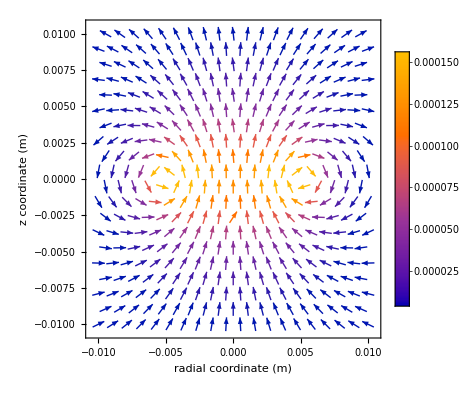

```mathematica
VectorPlot[{Bx,Bz}/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},{z,-0.01,0.01},PlotLegends->Automatic,FrameLabel->{"radial coordinate (m)","z coordinate (m)"}, VectorPoints->20](*vector plot to make sure everything is correct*)
```

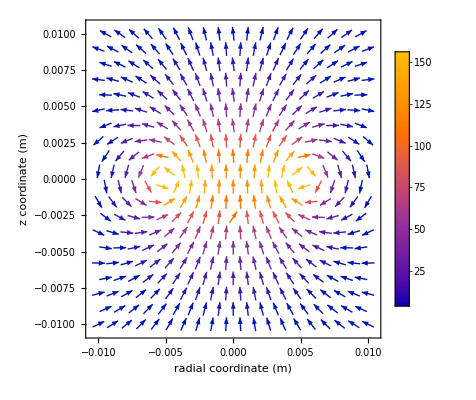

```mathematica
VectorPlot[{(10^6)Bx,(10^6)Bz}/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},{z,-0.01,0.01},PlotLegends->Automatic, FrameLabel->{"radial coordinate (m)","z coordinate (m)"}, VectorPoints->20](*vector plot to make sure everything is correct*)
```

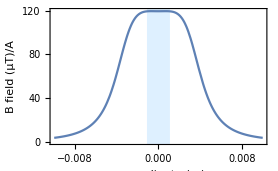

```mathematica
z=2*10^(-3);(*plotting off centre field*)
Plot[( Sqrt[(Norm[1000000Bx]^2) + (Norm[1000000Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},Frame->True,FrameLabel->{"x-coordinate (m)","B field (μT)/A"},Prolog->{LightBlue,Rectangle[{-0.0011,-10},{0.0011,10000}]}]
```

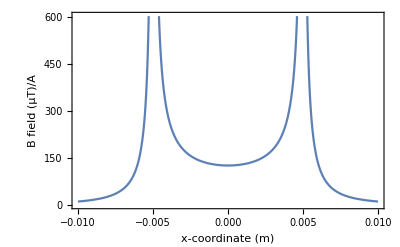

```mathematica
s=5*10^(-3);
z=0*10^(-3);(*plotting off centre field*)
Plot[( Sqrt[(Norm[1000000Bx]^2) + (Norm[1000000Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},Frame->{True,True,False,False},
FrameLabel->{"x-coordinate (m)","B field (μT)/A"}]
```

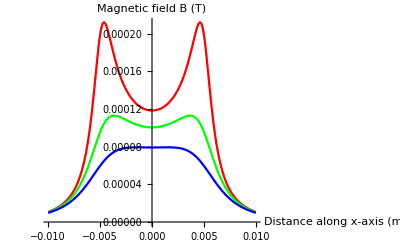

```mathematica
z=1*10^(-3);
one=Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm,PlotStyle->Red];
z=2*10^(-3);
two=Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm, PlotStyle->Green];
z=3*10^(-3);
three =Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm,PlotStyle->Blue];
Show[one,two,three]
```

```mathematica
z=2*10^(-3);
RevolutionPlot3D[( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},Mesh->30]
```

-Graphics3D-

```mathematica
s=3.25*10^(-3);
z=2*10^(-3);
one3d=RevolutionPlot3D[ ( Sqrt[(Norm[1000000*Bx]^2) + (Norm[1000000*Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"x-coordinate (m)","y-coordinate (m)","B field
 (μT)/A"},PlotStyle->Opacity[1],ColorFunction->Function[{x,y,z},Hue[0.65(1-z)]],Mesh->30]
```

-Graphics3D-

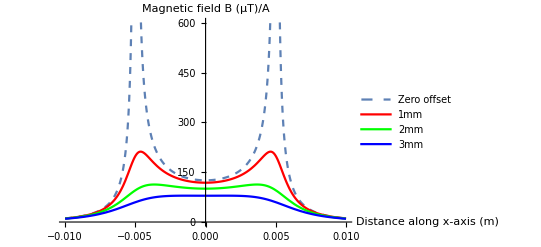

```mathematica
z=0*10^(-3);
zero=Plot[ ( Sqrt[(Norm[10^6Bx]^2) + (Norm[10^6Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (μT)/A"},AxesLabel->StandardForm,PlotStyle->Dashed,PlotLegends->{"Zero offset"}];
z=1*10^(-3);
one=Plot[ ( Sqrt[(Norm[10^6Bx]^2) + (Norm[10^6Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm,PlotStyle->Red,PlotLegends->{"1mm"}];
z=2*10^(-3);
two=Plot[ ( Sqrt[(Norm[10^6Bx]^2) + (Norm[10^6Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm, PlotStyle->Green,PlotLegends->{"2mm"}];
z=3*10^(-3);
three =Plot[ ( Sqrt[(Norm[10^6Bx]^2) + (Norm[10^6Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm,PlotStyle->Blue,PlotLegends->{"3mm"}];
Show[zero,one,two,three]
```

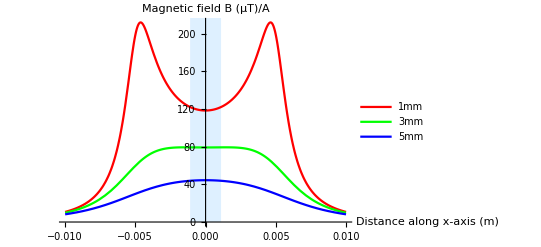

```mathematica
z=1*10^(-3);
one=Plot[ ( Sqrt[(Norm[10^6Bx]^2) + (Norm[10^6Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (μT)/A"},AxesLabel->StandardForm,PlotStyle->Red,PlotLegends->{"1mm"}];
z=3*10^(-3);
two=Plot[ ( Sqrt[(Norm[10^6Bx]^2) + (Norm[10^6Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm, PlotStyle->Green,PlotLegends->{"3mm"}];
z=5*10^(-3);
three =Plot[ ( Sqrt[(Norm[10^6Bx]^2) + (Norm[10^6Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},AxesLabel->{"Distance along x-axis (m)","Magnetic field B (T)"},AxesLabel->StandardForm,PlotStyle->Blue,PlotLegends->{"5mm"}];
Show[one,two,three,Prolog->{LightBlue,Rectangle[{-0.0011,0.000},{0.0011,250}]}]
```

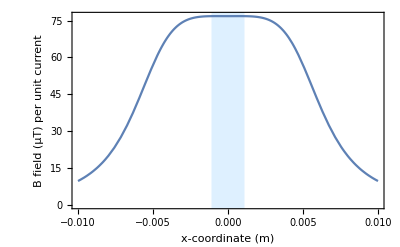

```mathematica
z=3.117*10^(-3);
Plot[ ( Sqrt[(Norm[1000000Bx]^2) + (Norm[1000000Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.01,0.01},Frame->True,FrameLabel->{"x-coordinate (m)","B field (μT) per unit current"},Prolog->{LightBlue,Rectangle[{-0.0011,-10},{0.0011,100}]}]
```

{{0.002867,0.314148},{0.002917,0.248509},{0.002967,0.184111},{0.003017,0.120973},{0.003067,0.059112},{0.003117,0.00145695},{0.003167,0.0607228},{0.003217,0.118677},{0.003267,0.175312},{0.003317,0.230624},{0.003367,0.284611}}

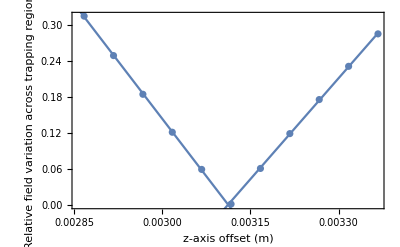

{1/200,a→0.003112}

```mathematica
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1.1*10^(-3);

z1 =(eyeball - 5*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
rel1=Abs[(edgeField-midField)/midField]*100;

z2 =(eyeball - 4*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
rel2=Abs[(edgeField-midField)/midField]*100;

z3 =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
rel3=Abs[(edgeField-midField)/midField]*100;

z4 =(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
rel4=Abs[(edgeField-midField)/midField]*100;

z5 =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
rel5=Abs[(edgeField-midField)/midField]*100;

z6 =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
rel6=Abs[(edgeField-midField)/midField]*100;

z7 =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
rel7=Abs[(edgeField-midField)/midField]*100;

z8 =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
rel8=Abs[(edgeField-midField)/midField]*100;

z9 =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
rel9=Abs[(edgeField-midField)/midField]*100;

z10 =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
rel10=Abs[(edgeField-midField)/midField]*100;

z11 =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
rel11=Abs[(edgeField-midField)/midField]*100;

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}}
linedecrease=Fit[relfield[[1;;5]],{1,a,a},a];
lineincrease=Fit[relfield[[7;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (m)","Relative field variation across trapping region (%)"},Frame->True,FrameLabel->{"z-axis offset (m)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5= {s,Zopt[[1,1]]}
```

```mathematica
s=6*10^(-3);(*now setting ring radius after integration*)
Bx
Bz
```

(Cot[θ] ((9/250000+ρ^2) EllipticE[(3 ρ Sin[θ])/(125 (9/250000+ρ^2+3/250 ρ Sin[θ]))]-EllipticK[(3 ρ Sin[θ])/(125 (9/250000+ρ^2+3/250 ρ Sin[θ]))] (9/250000+ρ^2-3/250 ρ Sin[θ])))/(5000000 (9/250000+ρ^2-3/250 ρ Sin[θ]) √(9/250000+ρ^2+3/250 ρ Sin[θ]))

((9/250000-ρ^2) EllipticE[(3 ρ Sin[θ])/(125 (9/250000+ρ^2+3/250 ρ Sin[θ]))]+EllipticK[(3 ρ Sin[θ])/(125 (9/250000+ρ^2+3/250 ρ Sin[θ]))] (9/250000+ρ^2-3/250 ρ Sin[θ]))/(5000000 (9/250000+ρ^2-3/250 ρ Sin[θ]) √(9/250000+ρ^2+3/250 ρ Sin[θ]))

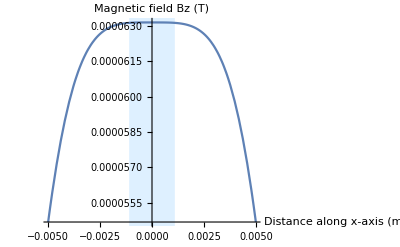

```mathematica
z=3.8*10^(-3);
Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.005,0.005},AxesLabel->{"Distance along x-axis (m)","Magnetic field Bz (T)"},Prolog->{LightBlue,Rectangle[{-0.0011,0.000},{0.0011,0.002}]}]
```

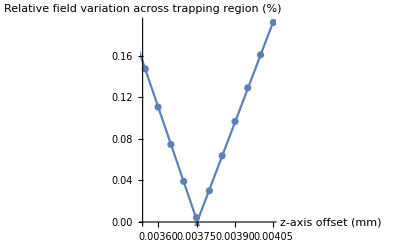

{3/500,a→0.00375296}

```mathematica
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1.1*10^(-3);

z1 =(eyeball - 5*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
rel1=Abs[(edgeField-midField)/midField]*100;

z2 =(eyeball - 4*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
rel2=Abs[(edgeField-midField)/midField]*100;

z3 =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
rel3=Abs[(edgeField-midField)/midField]*100;

z4 =(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
rel4=Abs[(edgeField-midField)/midField]*100;

z5 =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
rel5=Abs[(edgeField-midField)/midField]*100;

z6 =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
rel6=Abs[(edgeField-midField)/midField]*100;

z7 =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
rel7=Abs[(edgeField-midField)/midField]*100;

z8 =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
rel8=Abs[(edgeField-midField)/midField]*100;

z9 =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
rel9=Abs[(edgeField-midField)/midField]*100;

z10 =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
rel10=Abs[(edgeField-midField)/midField]*100;

z11 =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
rel11=Abs[(edgeField-midField)/midField]*100;

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;4]],{1,a,a},a];
lineincrease=Fit[relfield[[6;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5= {s,Zopt[[1,1]]}
```

```mathematica
s=7*10^(-3);(*now setting ring radius after integration*)
Bx
Bz
```

(Cot[θ] ((49/1000000+ρ^2) EllipticE[(7 ρ Sin[θ])/(250 (49/1000000+ρ^2+7/500 ρ Sin[θ]))]-EllipticK[(7 ρ Sin[θ])/(250 (49/1000000+ρ^2+7/500 ρ Sin[θ]))] (49/1000000+ρ^2-7/500 ρ Sin[θ])))/(5000000 (49/1000000+ρ^2-7/500 ρ Sin[θ]) √(49/1000000+ρ^2+7/500 ρ Sin[θ]))

((49/1000000-ρ^2) EllipticE[(7 ρ Sin[θ])/(250 (49/1000000+ρ^2+7/500 ρ Sin[θ]))]+EllipticK[(7 ρ Sin[θ])/(250 (49/1000000+ρ^2+7/500 ρ Sin[θ]))] (49/1000000+ρ^2-7/500 ρ Sin[θ]))/(5000000 (49/1000000+ρ^2-7/500 ρ Sin[θ]) √(49/1000000+ρ^2+7/500 ρ Sin[θ]))

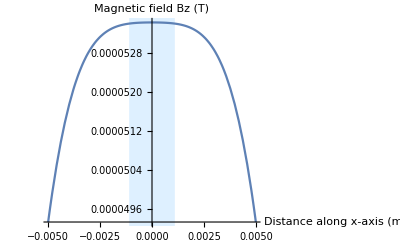

```mathematica
z=4.5*10^(-3);
Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.005,0.005},AxesLabel->{"Distance along x-axis (m)","Magnetic field Bz (T)"},Prolog->{LightBlue,Rectangle[{-0.0011,0.000},{0.0011,0.002}]}]
```

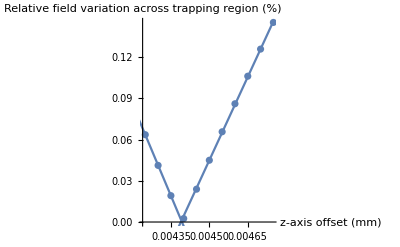

{7/1000,a→0.0043911}

```mathematica
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1.1*10^(-3);

z1 =(eyeball - 5*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
rel1=Abs[(edgeField-midField)/midField]*100;

z2 =(eyeball - 4*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
rel2=Abs[(edgeField-midField)/midField]*100;

z3 =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
rel3=Abs[(edgeField-midField)/midField]*100;

z4 =(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
rel4=Abs[(edgeField-midField)/midField]*100;

z5 =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
rel5=Abs[(edgeField-midField)/midField]*100;

z6 =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
rel6=Abs[(edgeField-midField)/midField]*100;

z7 =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
rel7=Abs[(edgeField-midField)/midField]*100;

z8 =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
rel8=Abs[(edgeField-midField)/midField]*100;

z9 =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
rel9=Abs[(edgeField-midField)/midField]*100;

z10 =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
rel10=Abs[(edgeField-midField)/midField]*100;

z11 =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
rel11=Abs[(edgeField-midField)/midField]*100;

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;3]],{1,a,a},a];
lineincrease=Fit[relfield[[5;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5= {s,Zopt[[1,1]]}
```

```mathematica
s=8*10^(-3);(*now setting ring radius after integration*)
Bx
Bz
```

(Cot[θ] ((1/15625+ρ^2) EllipticE[(4 ρ Sin[θ])/(125 (1/15625+ρ^2+2/125 ρ Sin[θ]))]-EllipticK[(4 ρ Sin[θ])/(125 (1/15625+ρ^2+2/125 ρ Sin[θ]))] (1/15625+ρ^2-2/125 ρ Sin[θ])))/(5000000 (1/15625+ρ^2-2/125 ρ Sin[θ]) √(1/15625+ρ^2+2/125 ρ Sin[θ]))

((1/15625-ρ^2) EllipticE[(4 ρ Sin[θ])/(125 (1/15625+ρ^2+2/125 ρ Sin[θ]))]+EllipticK[(4 ρ Sin[θ])/(125 (1/15625+ρ^2+2/125 ρ Sin[θ]))] (1/15625+ρ^2-2/125 ρ Sin[θ]))/(5000000 (1/15625+ρ^2-2/125 ρ Sin[θ]) √(1/15625+ρ^2+2/125 ρ Sin[θ]))

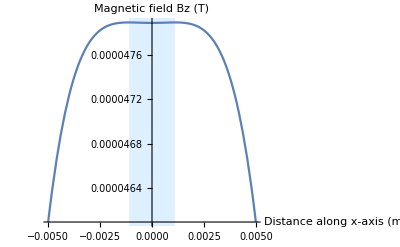

```mathematica
z=5*10^(-3);
Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.005,0.005},AxesLabel->{"Distance along x-axis (m)","Magnetic field Bz (T)"},Prolog->{LightBlue,Rectangle[{-0.0011,0.000},{0.0011,0.002}]}]
```

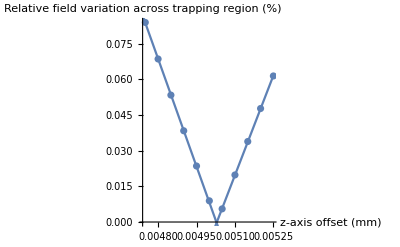

{1/125,a→0.00502843}

```mathematica
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1.1*10^(-3);

z1 =(eyeball - 5*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
rel1=Abs[(edgeField-midField)/midField]*100;

z2 =(eyeball - 4*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
rel2=Abs[(edgeField-midField)/midField]*100;

z3 =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
rel3=Abs[(edgeField-midField)/midField]*100;

z4 =(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
rel4=Abs[(edgeField-midField)/midField]*100;

z5 =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
rel5=Abs[(edgeField-midField)/midField]*100;

z6 =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
rel6=Abs[(edgeField-midField)/midField]*100;

z7 =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
rel7=Abs[(edgeField-midField)/midField]*100;

z8 =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
rel8=Abs[(edgeField-midField)/midField]*100;

z9 =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
rel9=Abs[(edgeField-midField)/midField]*100;

z10 =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
rel10=Abs[(edgeField-midField)/midField]*100;

z11 =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
rel11=Abs[(edgeField-midField)/midField]*100;

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;5]],{1,a,a},a];
lineincrease=Fit[relfield[[7;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5= {s,Zopt[[1,1]]}
```

```mathematica
s=9*10^(-3);(*now setting ring radius after integration*)
Bx
Bz
```

(Cot[θ] ((81/1000000+ρ^2) EllipticE[(9 ρ Sin[θ])/(250 (81/1000000+ρ^2+9/500 ρ Sin[θ]))]-EllipticK[(9 ρ Sin[θ])/(250 (81/1000000+ρ^2+9/500 ρ Sin[θ]))] (81/1000000+ρ^2-9/500 ρ Sin[θ])))/(5000000 (81/1000000+ρ^2-9/500 ρ Sin[θ]) √(81/1000000+ρ^2+9/500 ρ Sin[θ]))

((81/1000000-ρ^2) EllipticE[(9 ρ Sin[θ])/(250 (81/1000000+ρ^2+9/500 ρ Sin[θ]))]+EllipticK[(9 ρ Sin[θ])/(250 (81/1000000+ρ^2+9/500 ρ Sin[θ]))] (81/1000000+ρ^2-9/500 ρ Sin[θ]))/(5000000 (81/1000000+ρ^2-9/500 ρ Sin[θ]) √(81/1000000+ρ^2+9/500 ρ Sin[θ]))

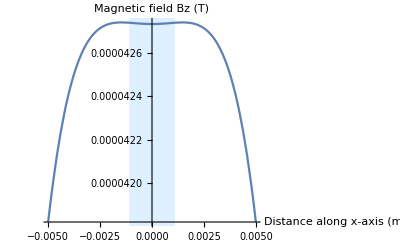

```mathematica
z=5.6*10^(-3);
Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.005,0.005},AxesLabel->{"Distance along x-axis (m)","Magnetic field Bz (T)"},Prolog->{LightBlue,Rectangle[{-0.0011,0.000},{0.0011,0.002}]}]
```

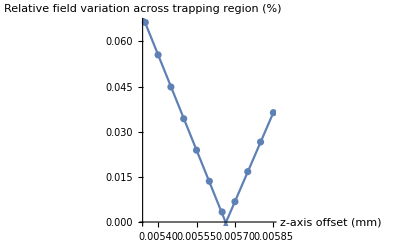

{9/1000,a→0.00566433}

```mathematica
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1.1*10^(-3);

z1 =(eyeball - 5*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
rel1=Abs[(edgeField-midField)/midField]*100;

z2 =(eyeball - 4*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
rel2=Abs[(edgeField-midField)/midField]*100;

z3 =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
rel3=Abs[(edgeField-midField)/midField]*100;

z4 =(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
rel4=Abs[(edgeField-midField)/midField]*100;

z5 =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
rel5=Abs[(edgeField-midField)/midField]*100;

z6 =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
rel6=Abs[(edgeField-midField)/midField]*100;

z7 =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
rel7=Abs[(edgeField-midField)/midField]*100;

z8 =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
rel8=Abs[(edgeField-midField)/midField]*100;

z9 =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
rel9=Abs[(edgeField-midField)/midField]*100;

z10 =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
rel10=Abs[(edgeField-midField)/midField]*100;

z11 =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
rel11=Abs[(edgeField-midField)/midField]*100;

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;6]],{1,a,a},a];
lineincrease=Fit[relfield[[8;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5= {s,Zopt[[1,1]]}
```

```mathematica
s=10*10^(-3);(*now setting ring radius after integration*)
Bx
Bz
```

(Cot[θ] ((1/10000+ρ^2) EllipticE[(ρ Sin[θ])/(25 (1/10000+ρ^2+1/50 ρ Sin[θ]))]-EllipticK[(ρ Sin[θ])/(25 (1/10000+ρ^2+1/50 ρ Sin[θ]))] (1/10000+ρ^2-1/50 ρ Sin[θ])))/(5000000 (1/10000+ρ^2-1/50 ρ Sin[θ]) √(1/10000+ρ^2+1/50 ρ Sin[θ]))

((1/10000-ρ^2) EllipticE[(ρ Sin[θ])/(25 (1/10000+ρ^2+1/50 ρ Sin[θ]))]+EllipticK[(ρ Sin[θ])/(25 (1/10000+ρ^2+1/50 ρ Sin[θ]))] (1/10000+ρ^2-1/50 ρ Sin[θ]))/(5000000 (1/10000+ρ^2-1/50 ρ Sin[θ]) √(1/10000+ρ^2+1/50 ρ Sin[θ]))

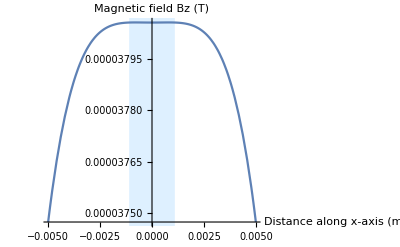

```mathematica
z=6.3*10^(-3);
Plot[ ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z,x],ρ->Sqrt[x^2+z^2]},{x,-0.005,0.005},AxesLabel->{"Distance along x-axis (m)","Magnetic field Bz (T)"},Prolog->{LightBlue,Rectangle[{-0.0011,0.000},{0.0011,0.002}]}]
```

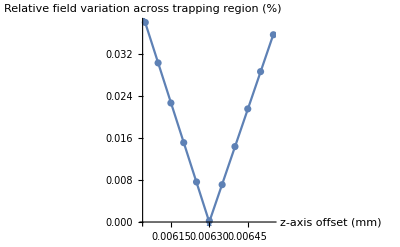

{1/100,a→0.0062997}

```mathematica
eyeball=z; (*the ballpark figure estimated using the plot above*)
it= 0.05*10^(-3) ;(*size of iterations*)
edge=1.1*10^(-3);

z1 =(eyeball - 5*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z1,x],ρ->Sqrt[x^2+z1^2]};
rel1=Abs[(edgeField-midField)/midField]*100;

z2 =(eyeball - 4*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z2,x],ρ->Sqrt[x^2+z2^2]};
rel2=Abs[(edgeField-midField)/midField]*100;

z3 =(eyeball  -3*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z3,x],ρ->Sqrt[x^2+z3^2]};
rel3=Abs[(edgeField-midField)/midField]*100;

z4 =(eyeball  -2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z4,x],ρ->Sqrt[x^2+z4^2]};
rel4=Abs[(edgeField-midField)/midField]*100;

z5 =(eyeball - 1*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z5,x],ρ->Sqrt[x^2+z5^2]};
rel5=Abs[(edgeField-midField)/midField]*100;

z6 =(eyeball - 0*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z6,x],ρ->Sqrt[x^2+z6^2]};
rel6=Abs[(edgeField-midField)/midField]*100;

z7 =(eyeball  +1*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z7,x],ρ->Sqrt[x^2+z7^2]};
rel7=Abs[(edgeField-midField)/midField]*100;

z8 =(eyeball  +2*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z8,x],ρ->Sqrt[x^2+z8^2]};
rel8=Abs[(edgeField-midField)/midField]*100;

z9 =(eyeball + 3*it);
x := 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
x :=edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z9,x],ρ->Sqrt[x^2+z9^2]};
rel9=Abs[(edgeField-midField)/midField]*100;

z10 =(eyeball  +4 *it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z10,x],ρ->Sqrt[x^2+z10^2]};
rel10=Abs[(edgeField-midField)/midField]*100;

z11 =(eyeball  + 5*it);
x = 0*10^(-3);
midField = Norm[Bz]/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
x =edge;
edgeField = ( Sqrt[(Norm[Bx]^2) + (Norm[Bz]^2)])/.{θ->ArcTan[z11,x],ρ->Sqrt[x^2+z11^2]};
rel11=Abs[(edgeField-midField)/midField]*100;

relfield={{z1,rel1},{z2,rel2},{z3,rel3},{z4,rel4},{z5,rel5},{z6,rel6},{z7,rel7},{z8,rel8},{z9,rel9},{z10,rel10},{z11,rel11}};
linedecrease=Fit[relfield[[1;;5]],{1,a,a},a];
lineincrease=Fit[relfield[[7;;11]] ,{1,a,a},a];

Show[ListPlot[relfield,AxesLabel->{"z-axis offset (mm)","Relative field variation across trapping region (%)"}],Plot[linedecrease,{a,0,z11}],Plot[lineincrease,{a,0,z11}]]

Zopt= Solve[{q==linedecrease,q==lineincrease},{a,q}];
Optimised5= {s,Zopt[[1,1]]}
```

-0.0732473+0.6375 r

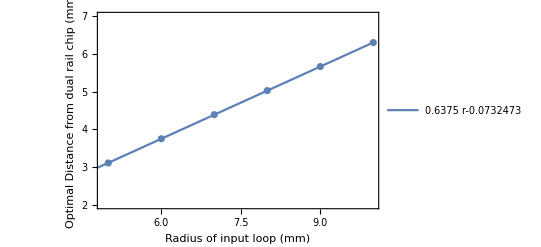

```mathematica
OptimiseData={{5,3.1114842425092955},{6,3.752961929858524},{7,4.39110285337617},{8,5.028425738018965},{9,5.664326749254793},{10,6.299698169265144}};
OptimisationFunc=Fit[OptimiseData,{1,r,r},r]

Show[ListPlot[OptimiseData,AxesLabel->{"Radius of input loop (mm)","Optimal Distance from dual rail chip (mm)"},Frame->True,FrameLabel->{"Radius of input loop (mm)","Optimal Distance from dual rail chip (mm)"},PlotRange->{2,7}],Plot[OptimisationFunc,{r,0,10},PlotLegends->{OptimisationFunc}]]
```

```mathematica
r=7 (*mm*); (*The radius of the input loop*)
Print["Optimal perpedicular distance from trap = ",OptimalRadius = OptimisationFunc," mm "]
Clear[r]
```

Optimal perpedicular distance from trap = 4.38925 mm